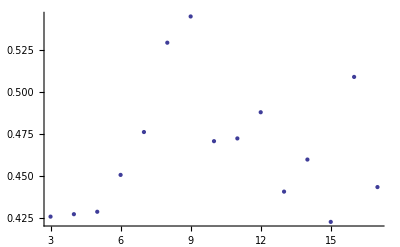

```mathematica
EPS=10^-10;
MySign=(If[#>EPS,1,If[#<-EPS,-1,0]])&;
LastColumn =Function[x,(#[[-1]])&/@Rest[x]];
Trend = (MySign/@(Rest[LastColumn[#]]-Most[LastColumn[#]]))&;
ListSum = Function[l,
MapIndexed[
Sum[l[[j]],{j,First[#2],First[Dimensions[l]]}]&,l]];
Ser=Table[ListSum[Trend[#1][[i;;i+#2-1]]],{i,1,First[Dimensions[Trend[#1]]]-#2}]&;
MyImport=Import["Documents/IMEMO/eurusd/"<>#, "TSV", "DateStringFormat" -> {"Year","-","Month","-", "Day","Hour",":","Minute",":","Second"}]&;

ColumnNames =Table[FromCharacterCode[{First[ToCharacterCode["a"]]+i-1}],{i,#}]&;
ColumnN =Table[i,{i,#}]&;

Cl1 = (If[#[[-1]]>=1,"m",If[#[[-1]]≤-1,"l","e"]])&;
Cl2 = (If[#≥3-EPS,"m",If[#≥2-EPS,"l","e"]])&;

InClass=Function[{l,s},Prepend[Map[Most[#]~Join~{Cl1[#]}&,Ser[l,s]],ColumnNames[s]]];

S = 5;
e1 =InClass[MyImport["EUR_USD.txt"], S];
e2 =InClass[MyImport["EUR_USD2.txt"], S];

<<weka`
LoadWeka[];


R =Table[e2 =InClass[MyImport["EUR_USD.txt"], S];e1 =InClass[MyImport["EUR_USD2.txt"], S];
m1=CreateWekaModel[e1, Most[ColumnN[S]],Last[ColumnN[S]],WekaAlgorithm->"MultilayerPerceptron"];r2 =Map[Cl2,RecallWekaModel[e2,m1]];r2r=Map[#[[-1]]&,Rest[e2]];c =MapThread[If[#1≠#2,0,1]&,{r2,r2r}];{S,N[Total[c]/First[Dimensions[c]]]},{S,3,17}];

ListPlot[R]
```